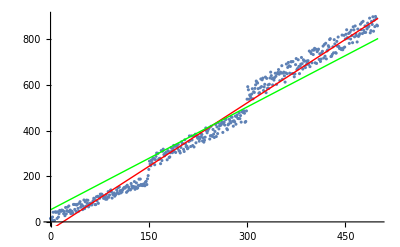

```mathematica
vertices = {};
For[x=0,x<500,x++,
y=x;
minErr = 0;
maxErr =40;
errAdd = 0;
errMult = 1.1;
If[x≥150,minErr=20; maxErr=80; errMult=1.4;];
If[x≥300,minErr=40; maxErr=120; errMult=1.6;];
(*Print[StringJoin[ToString[x]," ",ToString[minErr] , " " , ToString[maxErr]]];*)
If[maxErr≥0,errAdd=RandomInteger[{minErr,maxErr}];];
AppendTo[vertices,{x,errMult*y+errAdd}];
]
size = Length[vertices];

plotVertices = ListPlot[vertices];

(* A.alpha = y
To minimize (A.alpha - y) we solve the Gaussian Normal Equation:
(AT.A).alpha = AT.y
 *)

(* Define A, y *)
A = {};
y = {};
For[x=0,x<size,x++,
(* Indices are not zero based *)
AppendTo[A,{1,Part[vertices,x+1,1]}];
AppendTo[y,Part[vertices,x+1,2]];
]

(*Print[A];*)

(* Solve Gaussian Normal Equation
 LinearSolve[m,b] finds an x that solves m.x==b
 *)

alpha=LinearSolve[Transpose[A].A,Transpose[A].y];
(*Print[alpha];*)

linearRegr[x_] :=Part[alpha,2]x +Part[alpha,1];
plotLinearRegr = Plot[linearRegr[x],{x,0,size},PlotStyle->{{Red,Thick}}];

(* Tikhonov regularization includes a Tikhonov matrix Ti in minimization:
 A.beta - y + Ti.y
We need to solve:
(AT.A+TiT.Ti).beta = AT.y
*)
(* Use ConstantArray to generate a toeplitz matrix
*)
Ti = ConstantArray[{0,20},size];


beta = LinearSolve[Transpose[A].A+Transpose[Ti].Ti,Transpose[A].y];
tikhonovRegr[x_] :=Part[beta,2]x +Part[beta,1];
plotTikhonovRegr = Plot[tikhonovRegr[x],{x,0,size},PlotStyle->{{Green,Thick}}];

Show[plotVertices,plotLinearRegr,plotTikhonovRegr]
```

```mathematica
{}
```

{}